```mathematica
SetDirectory[NotebookDirectory[]]
shape=Import["shape.txt","Table"];
radius=ReadList["radius.txt",{Number,Number},RecordLists->True]
```

H:\Subversion\win\cpp\SC_FEM_Models\SC_FEM_Models\SCMapSeries

{{{0,-0.0557192},{1,0.0118809},{2,-0.0223043},{3,0.0401958},{4,0.0237256},{5,-5.69444×10^-8}}}

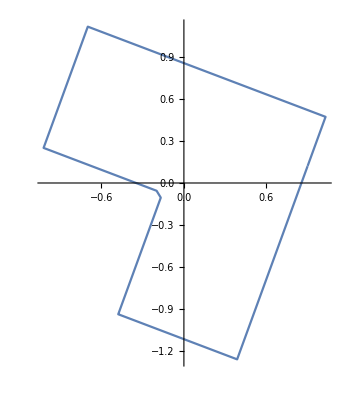

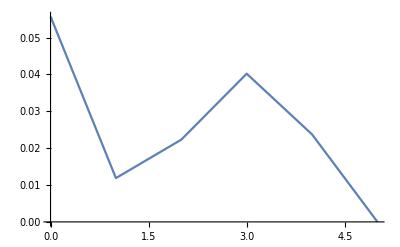

```mathematica
ListPlot[shape, Joined->True,AspectRatio->Automatic]
ListPlot[Abs[radius],Joined->True,PlotRange->All]
```